```mathematica
Off[LinearSolve::luc]
Off[$RecursionLimit::reclim2]
```

1)  set J and calc. (N̂)_ij^J and (Ĥ)_ij^J                      untainted/*.exe  boundstate with INQUA_N as in RHS calc.
2)

```mathematica
MUL=1;
pi="-";
LITham[hh_,nn_,σr_,σi_,B0_]:=Det[hh-(B0+σr+I σi) nn];
```

Setup of the RHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_deu]^Jm_J  (which is a vector!)

Setup of the LHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_deu]^Jm_J  

Read Norm  ( (Ν^J)_(l_n l_m))  and Hamilton  ( (Η^J)_(l_n l_m))  Matrix dimensionality for  J={0: N_1
1: N_0+N_1+N_2
2: N_1+N_2+N_3

```mathematica
LofM[jjJ_,mmJ_]:=Module[{mJ=mmJ,jJ=jjJ},
momentum=1;
sigmaI=5;smin=1;smax=100;nbrs=300;
sigmaRange=Range[smin,smax,(smax-smin)/nbrs];
file="~/kette_repo/ComptonLIT/av18_deuteron/norm-ham-litME-"<>ToString[jJ]<>pi;
NormHamMat=ReadList[file,Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
file="~/kette_repo/ComptonLIT/av18_deuteron/LIT_SOURCE_"<>ToString[jJ]<>pi<>ToString[mJ]<>ToString[MUL];
RHS=ReadList[file,Real,RecordLists->True];
Dimensions[norm];Dimensions[ham];
SlitDim=Dimensions[RHS[[1]]][[1]];
If[(JbasisDim==SlitDim)==False,
Print["Dim(Norm/H) ≠ Dim(S_LIT)"];
Print["Dim(Norm/H) = "<>ToString[JbasisDim]];
Print["Dim(S_LIT)   = "<>ToString[SlitDim]];
];
inhomo=RHS[[momentum]];
file="~/kette_repo/ComptonLIT/av18_deuteron/E0.dat";
Ed=Read[file];Close[file];
lOfSigma={};
For[n=1,n<nbrs,n++,(
(*Subscript[σ, r]=n;Subscript[σ, i]=5;σ=Subscript[σ, r]+I Subscript[σ, i];*)
coeff=LinearSolve[ham-Conjugate[sigmaRange[[n]]+sigmaI I] norm,inhomo];
lOfSigma=Append[lOfSigma,{sigmaRange[[n]],Conjugate[coeff].norm.coeff}];
)];
lOfSigma
]
```

```mathematica
Lm0=4 Pi Re[LofM[0,0]][[All,2]];
Lm1=4 Pi/3 Sum[Table[Re[LofM[1,m]],{m,-1,1}][[i]][[All,2]],{i,1,3}];
Lm2=4 Pi/5 Sum[Table[Re[LofM[2,m]],{m,-2,2}][[i]][[All,2]],{i,1,5}];
```

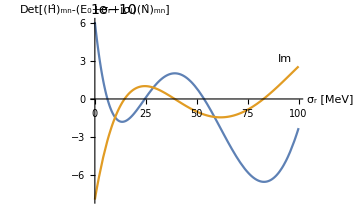
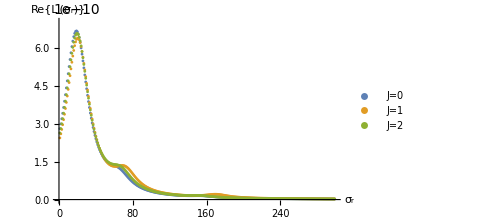
-Graphics- | -Graphics-E_0 = -1.6567 MeV

```mathematica
Labeled[Grid[
{{Plot[{Re[LITham[ham,norm,σr,sigmaI,Ed]],Im[LITham[ham,norm,σr,sigmaI,Ed]]},{σr,0,100},AxesLabel->{"σ_r [MeV]","Det[(Ĥ)_mn-(E_0+σ_r+iσ_i)(N̂)_mn]"},ImageSize->Medium,PlotLabels->Placed[{Re,Im},Above]]
,ListPlot[{Lm0,Lm1,Lm2},PlotLegends->Placed[{"J=0","J=1","J=2"},Above],AxesLabel->{"σ_r","Re{L_j(σ_r)}"},PlotRange->{Automatic,1.1 Max[Lm1]},ImageSize->Medium]}}],{"E_0 = "<>ToString[Ed]<>" MeV"},{Top}]
```

```mathematica
normmalcoeff=norm.coeff
normmalcoeff.coeff//MatrixForm
Conjugate[coeff].norm.coeff
```

{1.05785×10^-6+3.06049×10^-8 ⅈ,2.41402×10^-8+7.40847×10^-10 ⅈ,8.60316×10^-8+2.53363×10^-9 ⅈ,1.86044×10^-7+5.42301×10^-9 ⅈ,3.68715×10^-7+1.07022×10^-8 ⅈ,8.94637×10^-7+2.58962×10^-8 ⅈ}

1.36588×10^-12+7.91869×10^-14 ⅈ

1.36817×10^-12-1.31266×10^-27 ⅈ

```mathematica
ell=1;
m1=4;
m2=4;
(2 ell+1)!!/(2^(2+ell) (basisWidths[[ell+1]][[m1]]+basisWidths[[ell+1]][[m2]])^(1+ell)) Sqrt[Pi/(basisWidths[[ell+1]][[m1]]+basisWidths[[ell+1]][[m2]])]
```

0.0768279